# Drugi kviz

Vsaka podnaloga je vredna 1 točko, razen če je pri podnalogi zapisano drugače. Skupno je moč doseči 20 točk.

## Naloga 1

a)  Definirajte funkcijo , ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi produkt indeksa stolpca in indeksa vrstice (začnemo šteti z 1).

```mathematica
A[n_,m_]:=Table[i*j, {i,1,n}, {j,1,m}]
```

b) Pokažite, da je  simetrična matrika.

```mathematica
IsSymmetricMatrixQ[n_]:=Module[{M},M=A[n,n];
M ==Transpose[M]
]
```

c) Izračunajte lastne vrednosti in lastne vektorje matrike .

```mathematica
mat=A[10,10];
Eigenvalues[mat]
Eigenvectors[mat]
```

{385,0,0,0,0,0,0,0,0,0}

{{1,2,3,4,5,6,7,8,9,10},{-10,0,0,0,0,0,0,0,0,1},{-9,0,0,0,0,0,0,0,1,0},{-8,0,0,0,0,0,0,1,0,0},{-7,0,0,0,0,0,1,0,0,0},{-6,0,0,0,0,1,0,0,0,0},{-5,0,0,0,1,0,0,0,0,0},{-4,0,0,1,0,0,0,0,0,0},{-3,0,1,0,0,0,0,0,0,0},{-2,1,0,0,0,0,0,0,0,0}}

d) Izračunajte karakteristični polinom matrike .

```mathematica
CharacteristicPolynomial[mat,x]
```

-385 x^9+x^10

e) Matriko  diagonalizirajte. Določite ustrezno diagonalno matriko , prehodno matriko  in .

```mathematica
G=DiagonalMatrix[Eigenvalues[A[10,10]]]
P=Transpose[Eigenvectors[A[10,10]]]
Inverse[P]
```

{{385,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

{{1,-10,-9,-8,-7,-6,-5,-4,-3,-2},{2,0,0,0,0,0,0,0,0,1},{3,0,0,0,0,0,0,0,1,0},{4,0,0,0,0,0,0,1,0,0},{5,0,0,0,0,0,1,0,0,0},{6,0,0,0,0,1,0,0,0,0},{7,0,0,0,1,0,0,0,0,0},{8,0,0,1,0,0,0,0,0,0},{9,0,1,0,0,0,0,0,0,0},{10,1,0,0,0,0,0,0,0,0}}

{{1/385,2/385,3/385,4/385,1/77,6/385,1/55,8/385,9/385,2/77},{-2/77,-4/77,-6/77,-8/77,-10/77,-12/77,-2/11,-16/77,-18/77,57/77},{-9/385,-18/385,-27/385,-36/385,-9/77,-54/385,-9/55,-72/385,304/385,-18/77},{-8/385,-16/385,-24/385,-32/385,-8/77,-48/385,-8/55,321/385,-72/385,-16/77},{-1/55,-2/55,-3/55,-4/55,-1/11,-6/55,48/55,-8/55,-9/55,-2/11},{-6/385,-12/385,-18/385,-24/385,-6/77,349/385,-6/55,-48/385,-54/385,-12/77},{-1/77,-2/77,-3/77,-4/77,72/77,-6/77,-1/11,-8/77,-9/77,-10/77},{-4/385,-8/385,-12/385,369/385,-4/77,-24/385,-4/55,-32/385,-36/385,-8/77},{-3/385,-6/385,376/385,-12/385,-3/77,-18/385,-3/55,-24/385,-27/385,-6/77},{-2/385,381/385,-6/385,-8/385,-2/77,-12/385,-2/55,-16/385,-18/385,-4/77}}

f) (2 točki) Rešite matrično enačbo .

```mathematica
X= LinearSolve[A[10,10] + P-G,IdentityMatrix[10]]
A[10,10].X+P.X==G.X+IdentityMatrix[10]//Simplify
```

{{-53/20251,664/20251,534/20251,404/20251,274/20251,144/20251,2/2893,-116/20251,-246/20251,-376/20251},{4/20251,-7692/20251,-6918/20251,-6144/20251,-5370/20251,-4596/20251,-546/2893,-3048/20251,-2274/20251,18751/20251},{18/101255,-34614/101255,-31131/101255,-27648/101255,-4833/20251,-20682/101255,-2457/14465,-13716/101255,91022/101255,-1350/20251},{16/101255,-30768/101255,-27672/101255,-24576/101255,-4296/20251,-18384/101255,-2184/14465,89063/101255,-9096/101255,-1200/20251},{2/14465,-3846/14465,-3459/14465,-3072/14465,-537/2893,-2298/14465,12554/14465,-1524/14465,-1137/14465,-150/2893},{12/101255,-23076/101255,-20754/101255,-18432/101255,-3222/20251,87467/101255,-1638/14465,-9144/101255,-6822/101255,-900/20251},{2/20251,-3846/20251,-3459/20251,-3072/20251,17566/20251,-2298/20251,-273/2893,-1524/20251,-1137/20251,-750/20251},{8/101255,-15384/101255,-13836/101255,88967/101255,-2148/20251,-9192/101255,-1092/14465,-6096/101255,-4548/101255,-600/20251},{6/101255,-11538/101255,90878/101255,-9216/101255,-1611/20251,-6894/101255,-819/14465,-4572/101255,-3411/101255,-450/20251},{4/101255,93563/101255,-6918/101255,-6144/101255,-1074/20251,-4596/101255,-546/14465,-3048/101255,-2274/101255,-300/20251}}

True

g) Ali je matrika  obrnljiva?

```mathematica
A[n_,m_]:=Table[i*j, {i,1,n}, {j,1,m}]
Det[A[10,10]]==0
```

True

## Naloga 2

Imamo klančino z naklonom 20 stopinj dolžine 5m. Na dnu klančine se nahaja ravnina dolžine 10m.
Kroglico z radijem 20cm potisnemo s skrajno desnega roba ravnine s hitrostjo v0 = 11m/s. Ko pride kroglica na vrh klančine, skoči čez rob, dokler ne pristane na tleh (poševni met). 
Predpostavite lahko, da med kroglico in podlago ni trenja in da se zaradi kotaljenja energija ne izgublja. Simulirajte gibanje kroglice do trenutka ko pristane na tleh.
Za gravitacijski pospešek vzemite g = 9.81 m/s^2, za simulacijo pa vzemite  . (Glej sliko).

a) Definiraj gravitacijski pospešek, naklon, dolžino klanca, dolžino podlage, začetno hitrost in radij kroglice.

```mathematica
g=9.81;
kot=Pi/9;
dp=10;
d=5;
v0=11;
r=0.2;
```

b) Nariši klančino in tla.

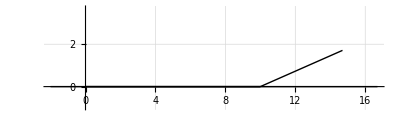

```mathematica
flatStart={0,0};
flatEnd={dp,0};
rampEnd=flatEnd+{d*Cos[kot],d*Sin[kot]};
Graphics[{Thick,Line[{flatStart,flatEnd}],Line[{flatEnd,rampEnd}],Line[{{-2,0},{rampEnd[[1]]+2,0}}] , Line[{flatStart,flatEnd}] },Axes->True,AxesOrigin->{0,0},AspectRatio->0.3,PlotRange->{{-2,rampEnd[[1]]+2},{-1,rampEnd[[2]]+2}},GridLines->Automatic]
```

c) Na sliko dodaj kroglico tako, da se bo kroglica premaknila, če se spremeni njeno središče (Uporabi `Dynamic`).

```mathematica
DynamicModule[{pos={-1,0.2}},Graphics[{Thick,Line[{{0,0},{10,0}}],Line[{{10,0},{10+5 Cos[Pi/9],5 Sin[Pi/9]}}],Line[{{-2,0},{20,0}}],Red,Disk[pos,0.2]},PlotRange->{{-2,20},{-1,5}},Axes->True]]
```

d) Definiraj funkcijo `naKlancu`, ki sprejme središče kroglice in vrne `True`, če je kroglica na klancu.

```mathematica
naKlancu[{x_,y_}]:=Module[{x1=10,x2=10+5 Cos[Pi/9]},x>=x1&&x<=x2]
```

e) Definiraj funkcijo `posodobiHitrost`, ki sprejme vektor trenutne hitrost kroglice in kot α ter vrne novo hitrost, gibanja po klančini z naklonom α po času Δt.

```mathematica
posodobiHitrost[v_,alpha_,dt_]:=
v+dt*g*{Cos[alpha], -Sin[alpha]}
```

f) Definiraj funkcijo `hitrostNaKlanec`, ki sprejme vektor trenutne hitrosti kroglice in kot α ter vrne novo hitrost, ki jo dobi kroglica, ko iz ravnega dela preide na klanec z naklonom α.

```mathematica
hitrostNaKlanec[v_,alpha_]:=Norm[v]*{Cos[alpha],Sin[alpha]}
```

g) Definiraj funkcijo `posodobiHitrostPosevniMet`, ki sprejme trenutno hitrost kroglice in vrne novo hitrost kroglice po času Δt.

```mathematica
posodobiHitrostPosevniMet[v_,dt_]:=v+dt*{0,-g}
```

h) Definiraj funkcijo `posodobiLego`, ki sprejme trenutno lego kroglice in njeno hitrost in vrne novo lego kroglice po času Δt.

```mathematica
posodobiLego[pos_,v_,dt_]:=pos+dt*v
```

i) S pomočjo prejšnjih funkcij simuliraj premikanje kroglice. (4 točke - gibanje po ravnini (1 točka), gibanje po klančini (1 točka), gibanje pri poševnem metu (1 točka), simulacija se ustavi, ko žogica pristane na tleh (1 točka))

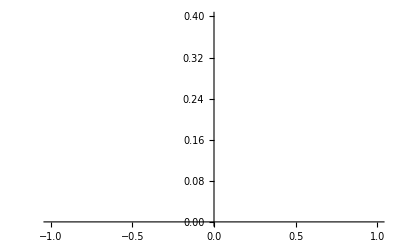

```mathematica
g=9.81;
kot=Pi/9;
dp=10;
d=5;
v0=11;
r=0.2;

simulateBall[]:=
Module[{dt=0.001,alpha=Pi/9,t=0,pos={0,0.2},v={11,0},trajectory={}},While[pos[[2]]>=0,AppendTo[trajectory,pos];
If[pos[[1]]<10,pos=posodobiLego[pos,v,dt];,
If[naKlancu[pos],v=posodobiHitrost[v,alpha,dt];
pos=posodobiLego[pos,v,dt];,
v=uposodobiHitrostPosevniMet[v,dt];
pos=posodobiLego[pos,v,dt];]];
t+=dt;];
trajectory]
ListLinePlot[simulateBall[]]
```